```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sohr/Documents/spring_2018_boulder/SRC_EXE_DIR/SOHR/projects/catalytic_cycle/theory/wall_S_chattering_problem

## A⇌_k2^k1 B⟶^k3 C problem

### Solve differential equation like d[A]/dt=-k1[A]+k2[B] d[B]/dt=k1[A]-k2[B]-k3[B] d[C]/dt=k3[B]

```mathematica
(*left hand side of equation in terms of k1, k2, k3 and t*)
LHS[k1_,k2_,t_,k3_]:=
Module[{soln,output,x1,x2,x3},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] - (k2 +k3)* x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
output=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
Return[output];]
(*left hand side of equation in terms of λ1, λ2, k3 and λ3, where λ1=k3/k1, λ2=k3/k2, λ3=k3*t*)
LHSLambda[λ1_,λ2_,λ3_,k3_]:=
Module[{soln,output,x1,x2,x3,k1,k2,t},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] - (k2 +k3) * x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
output=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
output = Simplify[output/.{k1->k3/λ1,k2->k3/λ2, t->λ3/k3},Assumptions->{k1>0,k2>0,k3>0,t>0}];
Return[output];]
(*Effective K*)
EffK[k1_,k2_,t_,k3_]:=
Module[{soln,output,x1,x2,x3},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] -(k2 +k3)* x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
output=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
output=Simplify[Log[output]/(-(t)), Assumptions->{k1>0,k2>0,k3>0,t>0}];
Return[output];]
(*Effective K in terms of lambda*)
EffKLambda[λ1_,λ2_,λ3_,k3_]:=
Module[{soln,output,x1,x2,x3,k1,k2,t},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] -(k2 +k3) * x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
output=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
output = Simplify[output/.{k1->k3/λ1,k2->k3/λ2, t->λ3/k3},Assumptions->{k1>0,k2>0,k3>0,t>0}];
output=Simplify[Log[output]/(-(λ3/k3)), Assumptions->{λ1>0,λ2>0,k3>0,λ3>0}];
Return[output];]
(*LHS2=Simplify[LHS/.{√(k1^2+4 k1 k2-2 k1 k3+k3^2)->Δ},Assumptions->{k1>0,k2>0,k3>0,t>0}]*)
```

```mathematica
Clear[λ1,λ2,λ3,k3];Series[Log[1-LHSLambda[λ1,λ2,λ3,k3]],{λ3,0,2}]
```

-2.22045×10^-16-(1. (-1.11022×10^-16 λ1+1. λ1^2+2. λ1 λ2+2. λ1^2 λ2+1. λ2^2-2. λ1 λ2^2+1. λ1^2 λ2^2) λ3)/(1. λ1^2+2. λ1 λ2+2. λ1^2 λ2+1. λ2^2-2. λ1 λ2^2+1. λ1^2 λ2^2)+1/2 (-(1. (-1.11022×10^-16 λ1+1. λ1^2+2. λ1 λ2+2. λ1^2 λ2+1. λ2^2-2. λ1 λ2^2+1. λ1^2 λ2^2)^2)/((1. λ1^2+2. λ1 λ2+2. λ1^2 λ2+1. λ2^2-2. λ1 λ2^2+1. λ1^2 λ2^2)^2)+(2. (-5.55112×10^-17 λ1+0.5 λ1^2-5.55112×10^-17 λ2+1. λ1 λ2+1.5 λ1^2 λ2-5.55112×10^-17 λ1 √(-4/λ1+(1+1/λ1+1/λ2)^2) λ2+0.5 λ2^2-2.22045×10^-16 λ1 λ2^2+1.5 λ1^2 λ2^2+0.5 λ2^3-1. λ1 λ2^3+0.5 λ1^2 λ2^3-5.55112×10^-17 λ1 √(-4/λ1+(1+1/λ1+1/λ2)^2) λ2^3-5.55112×10^-17 λ1^2 √(-4/λ1+(1+1/λ1+1/λ2)^2) λ2^3))/(λ2 (1. λ1^2+2. λ1 λ2+2. λ1^2 λ2+1. λ2^2-2. λ1 λ2^2+1. λ1^2 λ2^2))) λ3^2+O[λ3]^3

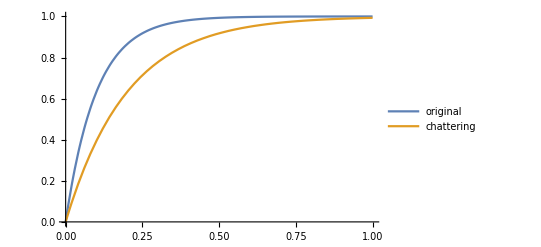

```mathematica
Plot[{1-ⅇ^(-k4*t)/.{k4->10^13},LHS[k1,k2,t,k3]/.{k1->10^25,k2->10^25,k3->10^13}//Evaluate},{t,0, 10^-12},PlotLegends->{"original","chattering"}]
```

```mathematica
LHS[k1,k2,t,k3]
```

(1. ⅇ^(-1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) (-0.5 k1^2-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k1^2+1. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k1^2-1. k1 k2-1. ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k1 k2+2. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k1 k2-0.5 k2^2-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k2^2+1. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k2^2+1. k1 k3+1. ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k1 k3-2. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k1 k3-1. k2 k3-1. ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k2 k3+2. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k2 k3-0.5 k3^2-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k3^2+1. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k3^2+0.5 k1 √(-4 k1 k3+(k1+k2+k3)^2)-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k1 √(-4 k1 k3+(k1+k2+k3)^2)+0.5 k2 √(-4 k1 k3+(k1+k2+k3)^2)-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k2 √(-4 k1 k3+(k1+k2+k3)^2)-0.5 k3 √(-4 k1 k3+(k1+k2+k3)^2)+0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k3 √(-4 k1 k3+(k1+k2+k3)^2)))/(1. k1^2+2. k1 k2+1. k2^2-2. k1 k3+2. k2 k3+1. k3^2)

```mathematica
LHSLambda[λ1,λ2,λ3,k3]
```

-1/(λ1 (2.-2. λ2) λ2+1. λ2^2+1. λ1^2 (1.+1. λ2)^2)0.5 ⅇ^(-((λ1+λ2+λ1 λ2+λ1 √(-4/λ1+(1+1/λ1+1/λ2)^2) λ2) λ3)/(2 λ1 λ2)) ((1.+1. ⅇ^(√(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2) λ3)-2. ⅇ^(((λ1+λ2+λ1 λ2+λ1 λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)) λ3)/(2 λ1 λ2))) λ2^2+1. λ1 λ2 (2.-2. λ2+ⅇ^(((λ1+λ2+λ1 λ2+λ1 λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)) λ3)/(2 λ1 λ2)) (-4.+4. λ2)-1. λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)+1. ⅇ^(√(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2) λ3) (2.-2. λ2+1. λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)))-1. λ1^2 (-1.-2. λ2-1. λ2^2+2. ⅇ^(((λ2+λ1 (1+λ2+λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2))) λ3)/(2 λ1 λ2)) (1.+1. λ2)^2+1. λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)-1. λ2^2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)+1. ⅇ^(√(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2) λ3) (-1.+λ2 (-2.-1. √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2))+λ2^2 (-1.+1. √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)))))